```mathematica
f[y_,ϵ_]:=1/(1+ϵ y)^(3/2)
y[ϵ_]:=Subscript[y, 0]+ϵ Subscript[y, 1]+ϵ^2 Subscript[y, 2]
F[ϵ_]:=f[y[ϵ],ϵ]
Series[F[ϵ], {ϵ,0,3}]
D[f[y,ϵ],ϵ]
```

1-(3 y_0 ϵ)/2+((15 y_0^2)/8-(3 y_1)/2) ϵ^2+1/16 (-35 y_0^3+60 y_0 y_1-24 y_2) ϵ^3+O[ϵ]^4

-(3 y)/(2 (1+y ϵ)^(5/2))

```mathematica
Clear[x,α,coefs,fractionalCoefs]
α=1/3;
x[ϵ_]:= Subscript[x, 0]+ϵ^α Subscript[x, 1]+ϵ^(2α) Subscript[x, 2]
coefs=Collect[Expand[(x[ϵ]+1)^3-ϵ x[ϵ] ],ϵ,Simplify]
fractionalCoefs=Most[Coefficient[coefs,ϵ,#]==0&/@Exponent[coefs,ϵ,List]]
MatrixForm[fractionalCoefs]
Solve[fractionalCoefs]
```

(1+x_0)^3+3 ϵ^(1/3) (1+x_0)^2 x_1+ϵ^2 x_2^3+3 ϵ^(2/3) (1+x_0) (x_1^2+(1+x_0) x_2)+ϵ^(5/3) x_2 (-1+3 x_1 x_2)+ϵ^(4/3) (-x_1+3 x_1^2 x_2+3 (1+x_0) x_2^2)+ϵ (x_1^3+6 x_1 x_2+x_0 (-1+6 x_1 x_2))

{(1+x_0)^3==0,3 (1+x_0)^2 x_1==0,3 (1+x_0) (x_1^2+(1+x_0) x_2)==0,x_1^3+6 x_1 x_2+x_0 (-1+6 x_1 x_2)==0,-x_1+3 x_1^2 x_2+3 (1+x_0) x_2^2==0,x_2 (-1+3 x_1 x_2)==0}

((1+x_0)^3==0
3 (1+x_0)^2 x_1==0
3 (1+x_0) (x_1^2+(1+x_0) x_2)==0
x_1^3+6 x_1 x_2+x_0 (-1+6 x_1 x_2)==0
-x_1+3 x_1^2 x_2+3 (1+x_0) x_2^2==0
x_2 (-1+3 x_1 x_2)==0)

{{x_0→-1,x_1→-1,x_2→-1/3},{x_0→-1,x_1→(-1)^(1/3),x_2→-1/3 (-1)^(2/3)},{x_0→-1,x_1→-(-1)^(2/3),x_2→1/3 (-1)^(1/3)}}

```mathematica
Solve[{(1+Subscript[x, 0])^3==0,-Subscript[x, 1]+3 (1+Subscript[x, 0]) Subscript[x, 1]^2+3 (1+Subscript[x, 0])^2 Subscript[x, 2]==0,Subscript[x, 1]^3-Subscript[x, 2]+6 (1+Subscript[x, 0]) Subscript[x, 1] Subscript[x, 2]==0,3 Subscript[x, 2] (Subscript[x, 1]^2+(1+Subscript[x, 0]) Subscript[x, 2])==0,3 Subscript[x, 1] Subscript[x, 2]^2==0}]
```

{{x_0→-1,x_1→0,x_2→0}}

```mathematica
α=1/2;
x[ϵ_]:= Subscript[x, 0]+ϵ^α Subscript[x, 1]+ϵ^(2α) Subscript[x, 2]
coefs=Collect[Expand[(x[ϵ]-1)^2+ϵ ],ϵ,Simplify];
fractionalCoefs=Most[Coefficient[coefs,ϵ,#]==0&/@Exponent[coefs,ϵ,List]];
MatrixForm[fractionalCoefs]
Solve[fractionalCoefs]
```

((-1+x_0)^2==0
2 (-1+x_0) x_1==0
1+x_1^2+2 (-1+x_0) x_2==0
2 x_1 x_2==0)

{{x_0→1,x_1→-ⅈ,x_2→0},{x_0→1,x_1→ⅈ,x_2→0}}

```mathematica
Clear[α,ϵ,x]
α=1;
x[ϵ_]:= Subscript[x, 0]+ϵ^α Subscript[x, 1]+ϵ^(2α) Subscript[x, 2]
coefs=Collect[Expand[x[ϵ]^3-(4+ϵ)x[ϵ]+2ϵ],ϵ,Simplify]
fractionalCoefs=Most[Coefficient[coefs,ϵ,#]==0&/@Exponent[coefs,ϵ,List]]
MatrixForm[fractionalCoefs]
Solve[fractionalCoefs]
Solve[a^3-4a==0,a]
```

x_0 (-4+x_0^2)+ϵ (2-x_0-4 x_1+3 x_0^2 x_1)+3 ϵ^5 x_1 x_2^2+ϵ^6 x_2^3+3 ϵ^4 x_2 (x_1^2+x_0 x_2)+ϵ^2 (-x_1+3 x_0 x_1^2+(-4+3 x_0^2) x_2)+ϵ^3 (x_1^3-x_2+6 x_0 x_1 x_2)

{x_0 (-4+x_0^2)==0,2-x_0-4 x_1+3 x_0^2 x_1==0,-x_1+3 x_0 x_1^2+(-4+3 x_0^2) x_2==0,x_1^3-x_2+6 x_0 x_1 x_2==0,3 x_2 (x_1^2+x_0 x_2)==0,3 x_1 x_2^2==0}

(x_0 (-4+x_0^2)==0
2-x_0-4 x_1+3 x_0^2 x_1==0
-x_1+3 x_0 x_1^2+(-4+3 x_0^2) x_2==0
x_1^3-x_2+6 x_0 x_1 x_2==0
3 x_2 (x_1^2+x_0 x_2)==0
3 x_1 x_2^2==0)

{{x_0→2,x_1→0,x_2→0}}

{{a→-2},{a→0},{a→2}}

```mathematica
Solve[{Subscript[x, 0] (-4+Subscript[x, 0]^2)==0,2-Subscript[x, 0]-4 Subscript[x, 1]+3 Subscript[x, 0]^2 Subscript[x, 1]==0,-Subscript[x, 1]+3 Subscript[x, 0] Subscript[x, 1]^2+(-4+3 Subscript[x, 0]^2) Subscript[x, 2]==0}]
```

{{x_0→-2,x_1→-1/2,x_2→1/8},{x_0→0,x_1→1/2,x_2→-1/8},{x_0→2,x_1→0,x_2→0}}

```mathematica
Clear[α,x]
α=1;
x[ϵ_]:= Subscript[x, 0]+ϵ^α Subscript[x, 1]+ϵ^(2α) Subscript[x, 2]
coefs=Collect[Expand[1/(1+ϵ x[ϵ])-x[ϵ]],ϵ,Simplify]
fractionalCoefs=Coefficient[coefs,ϵ,#]==0&/@Exponent[coefs,ϵ,List]
MatrixForm[fractionalCoefs]
Solve[fractionalCoefs]
```

-x_0-ϵ x_1-ϵ^2 x_2+1/(1+ϵ (x_0+ϵ x_1+ϵ^2 x_2))

{1-x_0==0,-x_1==0,-x_2==0}

(1-x_0==0
-x_1==0
-x_2==0)

{{x_0→1,x_1→0,x_2→0}}

```mathematica
Solve[E^Integrate[1/(1-u),u]==E^t,u]
```

{{u→ⅇ^-t (-1+ⅇ^t)}}

```mathematica
Clear[α,ϵ,g,c,dxx,dyy,v,u,x,y,xx,yy]
g= 10;
c=500;
α=0;
ϵ=0;
dxx=x''[t]==-ϵ x'[t]^2;
dyy=y''[t]==-ϵ x'[t]y'[t]-g;
DSolve[{dyy,y'[0]==v,y[0]==0},y,t]
DSolve[{dxx,x'[0]==u,x[0]==0},x,t]
```

{{y→Function[{t},-5 t^2+t v]}}

{{x→Function[{t},t u]}}

{{u→-349.964,v→-357.107,t→-1.42872},{u→349.964,v→357.107,t→1.42872},{u→-5.05129,v→-499.974,t→-98.9846},{u→5.05129,v→499.974,t→98.9846}}

{{v→(625000+u^2)/(250 u)}}

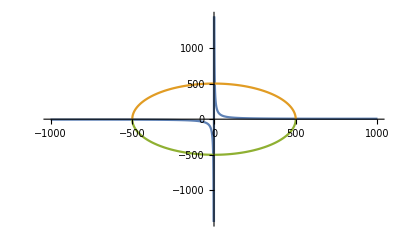

7.13928

9.80351

45.5788

89.4212

```mathematica
Clear[a,b,c,g]
a=500;b=2;c=500;g=10;
Solve[{a==u t,a== -(g t^2)/2+v t,u^2+v^2==c^2},{u,v,t}]//N
Solve[-1/2 g(a/u)^2+v(a/u)==b,v]
Plot[{v/.%,Sqrt[c^2-u^2],-Sqrt[c^2-u^2]},{u,-1000,1000}]
dy[t_,v_]:=-g t +v;
dx[t_,u_]:=u;
s[x_,y_]:=√(x^2+y^2);
s[dx[349.107,1.42872],dy[357.107,1.42872]]/c
s[dx[5.05129,98.9846],dy[499.974,98.9846]]/c
ArcTan[357.107/349.964]*180/Pi
ArcTan[499.974/5.05129]*180/Pi
```

integrate (x''=-x')

WolframAlphaQueryResults

derive x(t)=c*e^(-t)

WolframAlphaQueryResults

integrate x''=-x'

WolframAlphaQueryResults

```mathematica
Clear[u,w]
Expand[(u+ϵ w)^3]
```

u^3+3 u^2 w ϵ+3 u w^2 ϵ^2+w^3 ϵ^3

```mathematica
Simplify[DSolve[{y''[t]==x (g t-v),y[0]==0,y'[0]==0},y[t],t]]
D[%,t]
```

{{y[t]→1/6 t^2 (g t-3 v) x}}

{{y'[t]→1/6 g t^2 x+1/3 t (g t-3 v) x}}